ClearAll

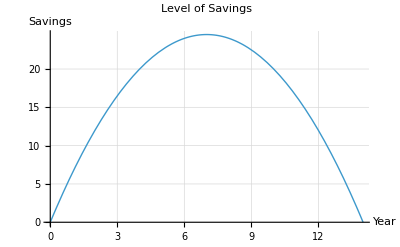

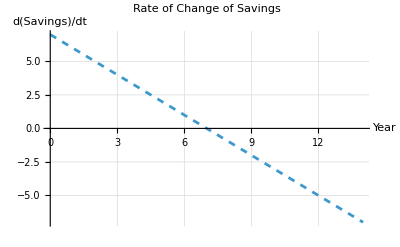

```mathematica
ClearAll

(*Parameters*)
T=14.0;
s0=0.0;
sT=0.0;
A=1; (*Positive for inverted U*)

(*Coefficients*)
c0=s0;
b=(sT-s0+0.5*A*T^2)/T;

(*Storage path as an explicit function*)
s[t_]:=-0.5*A*t^2+b*t+c0;

(*Derivative as an explicit function*)
dsdt[t_]:=-A*t+b;

(*Plot storage (inverted U)*)
Plot[
s[t],
{t,0,T},
PlotRange->All,
AxesLabel->{"Year","Savings"},PlotLabel->"Level of Savings",PlotStyle->Thick,GridLines->Automatic
]

(*Plot rate of change (line)*)
Plot[
dsdt[t],
{t,0,T},
PlotRange->All,
AxesLabel->{"Year","d(Savings)/dt"},PlotLabel->"Rate of Change of Savings",PlotStyle->Dashed,GridLines->Automatic
]
```